## Contour plot for the triaxial rotor

## 1-axis quantization: ℐ_1- maximal M.O.I

### Computing the contour plot for the triaxial nucleus when the first axis has the largest moment of inertia. The parameters must correspond to positive inertial factor A and positive k number.

## Functions

```mathematica
j1[j_,θ_]:=j*Cos[θ];
j2[j_,θ_]:=j*Sin[θ];
Afct[I_,a1_,a2_,j_,θ_]:=a2*(1-j2[j,θ]/I)-a1;
ufct[I_,a1_,a2_,a3_,j_,θ_]:=(a3-a1)/Afct[I,a1,a2,j,θ];
v0fct[I_,a1_,a2_,j_,θ_]:=-(a1*j1[j,θ])/Afct[I,a1,a2,j,θ];
kfct[I_,a1_,a2_,a3_,j_,θ_]:=Sqrt[ufct[I,a1,a2,a3,j,θ]];
IF[moi_]:=1/(2*moi);
j11=11/2;
```

## Energy Function

```mathematica
Hen[I_,a1_,a2_,a3_,j_,theta_,θ_,ϕ_]:=(Cos[ϕ]^2+ufct[I,a1,a2,a3,j,theta] Sin[ϕ]^2)I^2*Sin[θ]^2+2I*v0fct[I,a1,a2,j,theta]Cos[θ];
contour[I_,i1_,i2_,i3_,j_,theta_]:=ContourPlot[Hen[I,IF[i1],IF[i2],IF[i3],j,theta*π/180,θ,ϕ],{θ,0,π},{ϕ,-0.2,2π+0.2},PlotLegends->Automatic,Contours->14,FrameStyle->Directive[Black,Thick],FrameLabel->{"θ_1 [rad]","φ_1 [rad]"},LabelStyle->{18,Bold,Black,FontFamily->"Times New Roman"}];
```

## Numerical factors v_0 and k

```mathematica
Print[N[v0fct[19/2,IF[89],IF[12],j11,-71*π/180]]]
```

-0.170917

```mathematica
Print[N[ufct[19/2,IF[89],IF[12],IF[48],j11,-71*π/180]]]
```

0.081531

### Determine the saddle point (x_1,φ_1)=(v_o/u,π/2) - θ_1 coord

```mathematica
Print[N[ArcCos[N[v0fct[19/2,IF[89],IF[12],j11,-71*π/180]]/(N[ufct[19/2,IF[89],IF[12],IF[48],j11,-71*π/180]]*(19/2))]]]
```

1.7933

### Determine the maximum point (x_1,φ_1)=(v_o,0) - θ_1 coord

```mathematica
Print[N[ArcCos[N[v0fct[19/2,IF[89],IF[12],j11,-71*π/180]]/(19/2)]]]
```

1.58879

### First maximum point P1 for fixed φ_1

```mathematica
minimum[i1_,i2_,i3_,theta_,left_,right_]:=Print[NMinimize[{Hen[19/2,IF[i1],IF[i2],IF[i3],j11,theta*π/180,1.79329511873909,ϕ],ϕ≥left&&ϕ≤right},ϕ][[2,1]]];
minimum[89,12,48,-71,3,7]
```

ϕ→4.71239

### First maximum point P1 for fixed θ_1

```mathematica
maximum[i1_,i2_,i3_,theta_,left_,right_]:=Print[NMaximize[{Hen[19/2,IF[i1],IF[i2],IF[i3],j11,theta*π/180,1.5887885344756139,ϕ],ϕ≥left&&ϕ≤right},ϕ][[2,1]]];
maximum[89,12,48,-71,4,7]
```

ϕ→6.28319

### Draw a point on CP

```mathematica
(*saddle point*)
point1[θ_,text_,x_,y_]:=Graphics[{Red,PointSize[0.021],Point[{1.7932951187390973,θ}],Inset[Style[StringTemplate["``"][text],20,Bold,Italic,Red,FontFamily->"Times New Roman"],Scaled[{x,y}]]}];
(*maximum point*)
point2[ϕ_,text_,x_,y_]:=Graphics[{Blue,PointSize[0.021],Point[{1.5887885344756139,ϕ}],Inset[Style[StringTemplate["``"][text],20,Bold,Italic,Blue,FontFamily->"Times New Roman"],Scaled[{x,y}]]}];
```

### New parameters: check the positivity condition

#### FROM THE NUMERICAL FIT OF ^135Pr

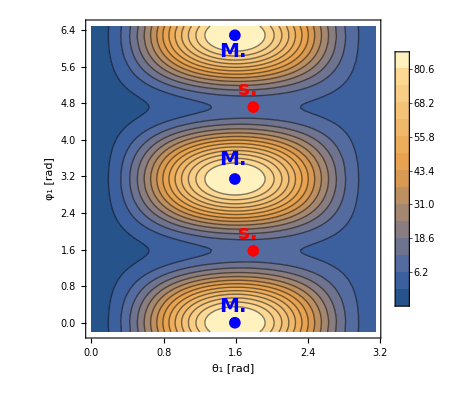

```mathematica
Show[contour[19/2,89,12,48,j11,-71],point2[0,"M.",0.5,0.1],point2[3.141592653589793,"M.",0.5,0.56],point2[6.283185307179586,"M.",0.5,0.9],point1[1.5707963267948966,"s.",0.55,0.33],point1[4.71238898038469,"s.",0.55,0.78]]
```